# The BayesianInference package

Load the package:

```mathematica
SetDirectory[NotebookDirectory[]];
<<BayesianInference`
```

## Nested Sampling

This package implements the nested sampling algorithm as described by John Skilling in his 2006 paper “Nested Sampling for General Bayesian Computation” (Bayesian Analysis, 1, number 4, pp. 833 - 860; available at ["http://citeseerx.ist.psu.edu/viewdoc/download?doi=10.1.1.117.5542&rep=rep1&type=pdf"](http://citeseerx.ist.psu.edu/viewdoc/download?doi=10.1.1.117.5542&rep=rep1&type=pdf)). There is also some functionality for ordinary Markov Chain Monte Carlo (MCMC) sampling.

The general workflow for using this package is as follows:

Define an inference problem using defineInferenceProblem. This returns an inferenceObject that contains all of the relevant  information needed for the next steps. defineInferenceProblem will do some sanity checks to try and anticipate problems further ahead

Use nestedSampling or parallelNestedSampling to run the algorithm on the inferenceObject

Use visualisation functions to interpret the result

### About the nested sampling algorithm

#### What is it good for?

The main goal of this package is to provide easy-to use code to do Bayesian inference with in Wolfram Language. The focus of the package is on the inference of distribution parameters from data and the computation of the evidence integral to compare different models of the data.

As a simple example of a problem, you could have a vector of numbers and you'd like to find out what distribution models these data:

```mathematica
data = {-0.11751148528054446,-2.191995254140541,-0.5143685660334552,0.2492396710667894,0.6840020913116259,3.0847964529819953,-0.5024324412173994,0.20244486030286893,0.4171228273329824,0.2541157610514157,-12.07292196121161,1.791517773009199,1.4615659758762654,-4.086822460322223,2.0862808562289623,-0.4356962558165376,1.3728589355070022,0.176323448749464,3.8047877638159977,1.5122102999265055};
Histogram[data]
```

The first idea is that these data could come from a normal distribution. A normal distribution has two free parameters that you would need to estimate:

```mathematica
distNormal =NormalDistribution[μ,σ]
```

The posterior distribution of μ and σ is given by, we know from Bayes’ rule that:

Pr[μ,σ\[Conditioned]Data]==(Likelihood[NormalDistribution[μ,σ], data]Pr[μ,σ])/Z

So to infer the posterior distribution, we need 3 things:

The likelihood function Likelihood[NormalDistribution[μ,σ], data], which is an unnormalised function of μ and σ. In this package, the likelihood is generally expressed as loglikelihood, because machine-precision arithmetic will often underflow when calculating the regular likelihood function. Whenever I mention the loglikelihood function in the context of this code package, I will always mean a function that:

Had the data “backed in” to it. The data is treated as a given and will always be part of the loglikelihood function and never an argument. This is primarily for efficiency reasons.

Accepts the parameters as a list like such:

```mathematica
logLikeFunction  = Function[{paramVector},Likelihood[NormalDistribution[paramVector[[1]],paramVector[[2]]], data]]
```

A prior distribution Pr[μ,σ]. In this package, the prior will always be converted to a log-PDF function that (just like the loglikelihood) accepts the parameters as a list.

The normalising constant Z, called the evidence (though in practise the quantity computed will be the log of the evidence). It is given by the multi-dimensional integral:

∫Likelihood[NormalDistribution[μ,σ], data]Pr[μ,σ]ⅆμ ⅆσ

The evidence is generally not analytically tractable and usually also difficult to approximate numerically with standard quadrature methods, which is a problem that the nested sampling algorithm specifically designed to solve. The evidence is a very useful quantity to know, though, because it’s a robust measure of model correctness for the data that automatically penalises a model for over-fitting. Thus, whenever the choice of model is uncertain, knowing the evidence for each will be of great help in model selection.

It should be note that an implicit assumption that is being made here is that the model parameters like μ and σ are continuous rather than discrete. This is the case for most inference problems, regardless of wether they are dealing with continuous data (like in this example) or nominal data (such as in classification). Classification is ultimately just regression of probabilities values, which are real values ∈[0, 1]. For example, the simplest nominal distribution is the BernoulliDistribution[p] , which is parameterised by the continuous variable p. Still, it is good to take note of the fact that the code in this package cannot deal with discrete model parameters directly; it is purely for dealing with continuous integration problems over the parameter space.

#### Basic code example

The model is defined like this:

```mathematica
normalModel =defineInferenceProblem[
"Data"-> data,
"GeneratingDistribution" -> distNormal,
"Parameters"->{{μ,-∞,∞},{σ,0,∞}},
"PriorDistribution"-> {NormalDistribution[0,100], ExponentialDistribution[1/100]}
]
```

The nested sampling algorithm is applied directly to the generated inferenceObject:

```mathematica
resultNormal=nestedSampling[normalModel,"MinMaxAcceptanceRate"->{0.1,0.9}]
resultNormal["LogEvidence"]
```

The histogram of the data suggest that the data has heavy tails, so perhaps a Cauchy distribution is more appropriate. Let’s compare the models:

```mathematica
distCauchy =CauchyDistribution[a,b];
cauchyModel =defineInferenceProblem[
"Data"-> data,
"GeneratingDistribution" -> distCauchy,
"Parameters"->{{a,-∞,∞},{b,0,∞}},
"PriorDistribution"-> {NormalDistribution[0,100], ExponentialDistribution[1/100]}
];
resultCauchy=nestedSampling[cauchyModel]
resultCauchy["LogEvidence"]
```

As you can see, the Cauchy model beats the normal model by about 5 points of logevidence or a factor of Exp[5]==148.413.

#### Brief explanation of the algorithm with interactive animation

The code below creates an animation visualising the process of generating samples from the posterior with the nested sampling algorithm:

```mathematica
dist=CauchyDistribution[0,1];
testdata=RandomVariate[dist,25];
obj =defineInferenceProblem[
"Data"-> testdata,
"GeneratingDistribution" -> CauchyDistribution[a, Exp[logb]],
"Parameters"->{{a,-10,10},{logb,-10,10}},
"PriorDistribution"-> {"LocationParameter", "LocationParameter"}
];
result =nestedSampling[
obj,
"SamplePoolSize"->100,
"MonteCarloSteps"->300,
"TerminationFraction" -> 0.01,
"MinMaxAcceptanceRate"->{0.1,0.9}
];
```

```mathematica
ClearAll[nestedSamplingAnimation];
nestedSamplingAnimation[result_, numberOfSlides :_Integer : 100, opts___]:=Module[{
samples=Values/@Values@Part[
KeySort@result["Samples"],
All,{"Point","LogLikelihood"}],
subset,
nLiveSamples=result["SamplePoolSize"],
logLikelihood = result["LogLikelihoodFunction"],
params = result["Parameters"]/.DirectedInfinity[sign_]:>sign * 10
},
Table[
subset=TakeDrop[SortBy[Last]@Take[samples,UpTo[n]],-nLiveSamples];
ContourPlot[
logLikelihood[result["ParameterSymbols"]],
Evaluate[Sequence@@result["Parameters"]],
opts,
FrameLabel->(Style[#,"Text",16]&)/@result["ParameterSymbols"],ImageSize->Large,
Epilog->
{
{Red,PointSize[0.01], Point[Rest@subset[[1,All,1]]],PointSize[0.025],Point[samples[[n+1,1]]]},
If[n>nLiveSamples,
{Black,PointSize[0.01],Point[Most@subset[[2,All,1]]],PointSize[0.025],Point[Last@subset[[2,All,1]]]},
Nothing
]
},
Contours->subset[[2,All,2]],
PlotLegends->Grid[{{Graphics[{Red,Disk[]},ImageSize->10],"Alive"},{Graphics[{Black,Disk[]},ImageSize->10],"Dead"}},BaseStyle->"Text",Alignment->Left]
],
{n,nLiveSamples,Min[nLiveSamples+numberOfSlides,Length[result["Samples"]]-1]}
]
];
```

```mathematica
slides = nestedSamplingAnimation[result,50];
ListAnimate[
slides,
AnimationRate->1
]
```

The new sample generated in each step is obtained by:

Picking one of the living samples at random. This already approximately samples the prior distribution if the living samples represent the prior well. Which they should, because the whole algorithm relies on that assumption.

Use Markov chain Monte Carlo (MCMC) to evolve the point and generate a new sample from a constrained version of the prior distribution. In simple terms, the prior density is set to zero wherever the loglikelihood function is less than the value of the worst currently living point.

What you see in the animation is a contour plot of the loglikelihood function. Only the contours corresponding to dead samples are drawn, so the bright area in the center is the area where the likelihood is high enough to allow new samples to be drawn. 

In this animation you can clearly see the shells corresponding to (approximately) constant loglikelihood values. The evidence is estimated by estimating the volume of the prior contained in each of these shells. To put it into cooking terms: instead of integrating the posterior by dicing the domain into squares (like most integration methods do) and multiplying the volume of each square with the function value, the nested sampling algorithm works by peeling off the loglikelihood function like an onion. The volume of each onion peel cannot be derived exactly; it’s only known statistically. This is why the logevidence is reported with a standard error.

### defineInferenceProblem and inferenceObject

Here’s a typical usage example of defineInferenceProblem corresponding to the problem of inferencing the parameters of a normal distribution:

```mathematica
obj=defineInferenceProblem[
"Data"-> RandomVariate[NormalDistribution[0,1],100],
"GeneratingDistribution" -> NormalDistribution[mu, sigma],
"Parameters"->{{mu,-∞,∞},{sigma,0,∞}},
"PriorDistribution"-> ProductDistribution[NormalDistribution[0,100],ExponentialDistribution[1/100]]
]
```

Note the tooltip on the inferenceObject that gives a summary of its contents. The inferenceObject is basically just a wrapper for an Association that holds all relevant information. It’s important to note, though, that due to its typesetting you cannot copy-paste it in a notebook:

This is intentional: if it was possible to copy-paste the object, it would be necessary to store potentially large amounts of data in the notebook, which would be slow.

This is how you check what properties are contained in the object:

```mathematica
obj["Properties"]
```

You can add information manually, even properties that are just for your own convenience:

```mathematica
obj = Append[obj, "Name"-> "Example"]
obj["Properties"]
```

To see what possible inputs there are for defining your problem, evaluate:

```mathematica
defineInferenceProblem[]
```

To run the nested sampling algorithm, we ultimately need to define the following properties:

Parameters: A list specifying the parameters that are to be estimated and their limits (which are allowed to be infinite)

LogLikelihoodFunction: a function (preferably compiled) that evaluates the loglikelihood at a given point in the parameter space

LogPriorPDFFunction: The logPDF function (preferably compiled) of the prior distribution (does not need to be normalised, but the computed evidence depends on its normalisation constant)

StartingPoints: A set of samples from the prior to use as a starting point

The role of defineInferenceProblem is to construct these properties from the properties supplied by the user. However, the you can forego the use of defineInferenceProblem by simply creating an association with the 4 required items and wrapping inferenceObject around it.

The convention that is used throughout this package, is that the n estimation parameters from an vector in nD space. For example, if the loglikelihood function is a function of 2 parameters, it should be of the form:

```mathematica
logLikelihood[paramVector_List]:= numericFunctionOf[paramVector[[1]],paramVector[[2]]];
```

Furthermore, the code works best if we stay within the realm of machine numbers. However, since the log of zero cannot be represented in machine numbers, the package uses a value called $MachineLogZero instead:

```mathematica
$MachineLogZero
```

This value should be returned whenever the point in parameter space is outside of the support of the prior or loglikelihood. If you use defineInferenceProblem to create the loglikelihood and logprior PDF, this is handled automatically:

```mathematica
obj["LogPriorPDFFunction"][{0,1}]
obj["LogPriorPDFFunction"][{0,-1}]
obj["LogLikelihoodFunction"][{0,-1}]
```

#### Known issues:

Please note that if you specify an explicit PriorDistribution, the limits specified by the parameters will cut off the prior without adjusting the normalisation constant of the prior PDF:

```mathematica
Table[
With[{
obj=defineInferenceProblem[
"Data"-> RandomVariate[NormalDistribution[0,1],100],
"GeneratingDistribution" -> NormalDistribution[mu, sigma],
"Parameters"->{{mu,-lim,lim},{sigma,0,lim}},
"PriorDistribution"-> ProductDistribution[NormalDistribution[0,100],ExponentialDistribution[1/100]]
]
},
Quiet@NIntegrate[
Exp@obj["LogPriorPDFFunction"][{x,y}],
{x,-∞,∞},
{y,0,∞}
]
],
{lim, {∞,10}}
]
```

When specifying the prior distribution as a list of distributions (in which case defineInferenceProblem will construct a ProductDistribution for you), the normalisation will be restored:

```mathematica
Table[
With[{
obj=defineInferenceProblem[
"Data"-> RandomVariate[NormalDistribution[0,1],100],
"GeneratingDistribution" -> NormalDistribution[mu, sigma],
"Parameters"->{{mu,-lim,lim},{sigma,0,lim}},
"PriorDistribution"-> {NormalDistribution[0,100],ExponentialDistribution[1/100]}
]
},
Quiet@NIntegrate[
Exp@obj["LogPriorPDFFunction"][{x,y}],
{x,-∞,∞},
{y,0,∞}
]
],
{lim, {∞,10}}
]
```

### General nested sampling problems

#### Fitting a Cauchy distribution

As a simple example, here is how you inference the parameters of a Cauchy distribution from some data.

```mathematica
dist=CauchyDistribution[0,1];
testdata=RandomVariate[dist,25];
obj =defineInferenceProblem[
"Data"-> testdata,
"GeneratingDistribution" -> CauchyDistribution[a, b],
"Parameters"->{{a,-100,100},{b,0.01,100}},
"PriorDistribution"-> {"LocationParameter", "ScaleParameter"},
"OriginalDistribution" -> dist (* This is an optional property that we attach for convenience *)
]
```

Note that the data has been transformed from a vector to a matrix as part of the standardisation process:

```mathematica
testdata
obj["Data"]
```

Run the algorithm with various options:

“MonteCarloSteps” determines how many MCMC steps to take to generate each new sample.

"MinMaxAcceptanceRate" determines the limits of the MCMC acceptance rate before the algorithm accepts a new sample. By default, no limits are imposed on the acceptance rate.

"TerminationFraction" determines how long the algorithm iterates before convergence is reached.

“MaxIterations” determines the maximum number of samples that will be generated.

“MinIterations” specifies the minimum number of nested samples that will be generated. For loglikelihood functions that are sharply peaked, it may be necessary to increase this option value to make sure the algorithm finds the bulk of the posterior.

“LogLikelihoodMaximum” allows the user to specify the maximum of the loglikelihood function if this is already known. Specifying this value will help the algorithm to determine when it should terminate.

```mathematica
result =nestedSampling[
obj,
"SamplePoolSize"->100,
"MonteCarloSteps"->300,
"TerminationFraction" -> 0.01,
"MinMaxAcceptanceRate"->{0.1,0.9}
]
result["LogEvidence"]
result["Properties"]
```

The standard error on the logevidence is obtained by Monte Carlo sampling of the X-axis values of the integral as described by Skilling in chapter 8 of his paper. The “PostProcessSamplingRuns” option controls how many such Monte Carlo samples are used to compute this standard error.

To speed up the computation, you can use parallelNestedSampling to divide the process over multiple kernels. Instead of having 100 living points, you can run 4 kernels with each 25 living points each (which each converge faster than 1 process with 100 points) for a comparable result:

```mathematica
result=parallelNestedSampling[
obj,
"SamplePoolSize"->25,
"ParallelRuns"->4,
"MonteCarloSteps"->300,
"TerminationFraction" -> 0.01,
"MinMaxAcceptanceRate"->{0.1,0.9}
]
result["LogEvidence"]
```

Use the calculationReport function to get a quick overview of the result:

```mathematica
calculationReport[result]
```

Visualise the posterior distribution of the parameters a and b:

```mathematica
Mean[result["EmpiricalPosteriorDistribution"]]
Covariance[result["EmpiricalPosteriorDistribution"]]
covarianceMatrixPlot[result]
posteriorBubbleChart[result,{a,b},
ScalingFunctions->{None,"Log",None},
PerformanceGoal-> "Speed"
]
```

Note that the bubble chart above is cluttered up with many samples with very small weights. You can use the function takePosteriorFraction to discard the samples with the smallest weights and retain the most important samples. In the example below, 1% of the posterior mass is discarded:

```mathematica
truncatedResult = takePosteriorFraction[result,0.99];
posteriorBubbleChart[
truncatedResult,{a,b},
ScalingFunctions->{None,"Log",None}
]
```

Plot the marginal PDFs of a and b:

```mathematica
posteriorMarginalPDFPlot1D[truncatedResult,a,ScalingFunctions->"Log", PlotRange->{{-5,5},{10^-6,All}}]
posteriorMarginalPDFPlot1D[truncatedResult,b,ScalingFunctions->{"Log","Log"},PlotRange->{{0.01,5},{10^-6,All}}]
```

Compare the original distribution that generated the data with the Bayesian predictive distribution:

```mathematica
LogPlot[
Evaluate[{
PDF[predictiveDistribution[truncatedResult],x],
PDF[predictiveDistribution[truncatedResult,"MaximumLikelihood"], x],
PDF[predictiveDistribution[truncatedResult,"MAP"], x],
PDF[result["OriginalDistribution"],x]
}],
{x,-10,10},
PlotRange->All,
PlotLegends->{"Posterior predictive PDF", "PDF based on maximum likelihood estimate","PDF based on maximum posterior (MAP) estimate", "PDF of original distribution"}
]
```

Compute the evidence of a competing model to see if it offers a better explanation of the data. In this case the evidence is significantly lower for model 2, so the Cauchy distribution explains the data better than a normal distribution:

```mathematica
obj2 =defineInferenceProblem[
"Data"-> testdata,
"GeneratingDistribution" -> NormalDistribution[a, b],
"Parameters"->{{a,-100,100},{b,0.01,100}},
"PriorDistribution"-> {"LocationParameter", "ScaleParameter"}
];
result2 =parallelNestedSampling[
obj2,
"MonteCarloSteps"->300,
"TerminationFraction" -> 0.01
]
result2["LogEvidence"]
```

```mathematica
LogPlot[
Evaluate[{
PDF[predictiveDistribution[result],x],
PDF[predictiveDistribution[result2],x],
PDF[result["OriginalDistribution"],x]
}],
{x,-10,10},
PlotRange->All,
PlotLegends->{"Posterior predictive PDF model 1", "Posterior predictive PDF model 2", "PDF of original distribution"}
]
```

#### MCMC

You can also sample the posterior directly. First create a MarkovChainObject for this problem with createMCMCChain:

```mathematica
dist=CauchyDistribution[0,1];
testdata=RandomVariate[dist,25];
obj =defineInferenceProblem[
"Data"-> testdata,
"GeneratingDistribution" -> CauchyDistribution[a, b],
"Parameters"->{{a,-100,100},{b,0.01,100}},
"PriorDistribution"-> {"LocationParameter", "ScaleParameter"},
"OriginalDistribution" -> dist (* This is an optional property that we attach for convenience *)
];
chain =createMCMCChain[obj,{0,1}(* starting point*)]
```

This function also accepts logPDF functions directly. Use compiled functions for the best performance:

```mathematica
chain=createMCMCChain[Compile[{{pt,_Real,1}},- pt. pt],{0,0}]
```

The MCMC sampler uses an adaptive algorithm that tries to learn the covariance of the distribution. Use the options of createMCMCChain to influence this behaviour:

```mathematica
Options[createMCMCChain]
```

Use iterateMCMC to sample the distribution. Note that this function changes the state of the chain:

```mathematica
iterateMCMC[chain,10000]; (* Burn it in first *)
samples=iterateMCMC[chain,1000];
```

```mathematica
Mean[samples]
Covariance[samples]
SmoothDensityHistogram[samples]
```

The MCMC methods are implemented in the Statistics`MCMC` context, which should be available in Mathematica 11.3.

View the methods available for Statistics`MCMC`BuildMarkovChain:

```mathematica
Statistics`MCMC`MCMCData[]
```

This package uses the {"AdaptiveMetropolis","Log"} method. Here’s how you view more detailed information about this method:

```mathematica
Statistics`MCMC`MCMCData[{"AdaptiveMetropolis","Log"},"Usage"]
Statistics`MCMC`MCMCData[{"AdaptiveMetropolis","Log"},"Example"]
```

Iteration of the Markov chain is done with Statistics`MCMC`MarkovChainIterate. It uses the following syntax:

```mathematica
Statistics`MCMC`MarkovChainIterate[MCobj,num of samples]
Statistics`MCMC`MarkovChainIterate[MCobj,{num of samples, number of iterations between each sample}]
```

#### Fitting Normal data with a SkewNormal distribution

```mathematica
dist=NormalDistribution[0,1];
testdata=RandomVariate[dist,50];
result=<||>;
```

```mathematica
dist=SkewNormalDistribution[0,1,1];
testdata=RandomVariate[dist,20];
result=<||>;
```

```mathematica
Plot[
Evaluate[{
PDF[NormalDistribution[0,1],x],
PDF[SkewNormalDistribution[0,1,1],x]
}],
{x,-3,3},
Filling->Axis
]
```

```mathematica
result["Normal"] = nestedSampling[
defineInferenceProblem[
"Data"-> testdata,
"GeneratingDistribution" -> NormalDistribution[a, b],
"Parameters"->{{a,-10,10},{b,0.1,10}},
"PriorDistribution"-> {"LocationParameter", "ScaleParameter"},
"OriginalDistribution" -> dist
],
"SamplePoolSize"->100,
"MonteCarloSteps"->300,
"TerminationFraction" -> 0.01,
"MaxIterations"->3000
]
```

```mathematica
result["SkewNormal"] = nestedSampling[
defineInferenceProblem[
"Data"-> testdata,
"GeneratingDistribution" -> SkewNormalDistribution[a, b, c],
"Parameters"->{{a,-10,10},{b,0.1,10},{c,-10,10}},
"PriorDistribution"-> {"LocationParameter", "ScaleParameter", "LocationParameter"},
"OriginalDistribution" -> dist
],
"SamplePoolSize"->100,
"MonteCarloSteps"->300,
"TerminationFraction" -> 0.01,
"MaxIterations"->3000
]
```

```mathematica
posteriorBubbleChart[takePosteriorFraction[result["Normal"],0.99],{a,b}]
posteriorBubbleChart[takePosteriorFraction[result["SkewNormal"],0.99],{a,b}]
posteriorBubbleChart[takePosteriorFraction[result["SkewNormal"],0.99],{a,b,c}]
```

```mathematica
Show[
Histogram[testdata,{0.1},"PDF"],
Plot[
Evaluate[{
PDF[predictiveDistribution[takePosteriorFraction[result["Normal"],0.99]],x],
PDF[predictiveDistribution[takePosteriorFraction[result["SkewNormal"],0.99]],x]
}],
{x,-4,4},
PlotRange->All,
Filling->Axis
],
PlotRange->All
]
```

#### Regression

Regression problems can be specified as well. First define some test data:

```mathematica
BlockRandom[
SeedRandom[1];
testdata=(#-> (#+2 RandomReal[]))&/@RandomReal[{-1,1},20];
ListPlot[List@@@testdata]
]
testdata
```

Note that the data is specified as a list of rules or as a rule of lists ({in1, in2, ...}→ {out1, out2, ...}) just like in "Predict"paclet:/ref/Predict.

The model is specified as a distribution that depends on an independent variable (note the standardisation of the data):

```mathematica
obj=defineInferenceProblem[
"Data"-> testdata,
"GeneratingDistribution" -> NormalDistribution[
a x + b,
sigma
],
"Parameters"->{{a,-10,10},{b,-10,10},{sigma,0.1,10}},
"IndependentVariables"-> {x},
"PriorDistribution"-> {"LocationParameter","LocationParameter", "ScaleParameter"}
]
obj["Data"]
```

The functions predictiveDistribution and regressionPlot1D are useful helper functions to visualise the results:

```mathematica
result=nestedSampling[obj]
predictions=predictiveDistribution[takePosteriorFraction[result,0.99],Range[-2,2,0.1]];
regressionPlot1D[result,predictions]
```

You can visualise the different lines that are used in this result:

```mathematica
With[{
result = takePosteriorFraction[result,0.99]
},
With[{
points = Values@result["Samples", All, "Point"],
weights = Values@Quiet@Exp[#-Max[#]&@result["Samples", All, "LogPosteriorWeight","Mean"]],
model =expressionToFunction[result["GeneratingDistribution", 1],result["ParameterSymbols"]]
},
Show[
Show @ MapThread[
Plot[Evaluate@model[#1],{x,-2,2},PlotStyle->Directive[Black,Opacity[#2]]]&,
{points,weights}
],
ListPlot[Transpose[List@@(Flatten/@result["Data"])],PlotStyle->Red]
]
]
]
```

Compare 3 polynomial models of increasing order:

```mathematica
variables[order_]:={
Sequence@@Table[{Symbol["c"<>ToString[i]],-100,100},{i,0,order}],
{s0,0.01,100}
};
result=
Association@Table[
order-> With[{
obj=With[{
vars = variables[order]
},
defineInferenceProblem[
"Data"-> testdata,
"GeneratingDistribution" -> NormalDistribution[
vars[[;;-2, 1]] . x^Range[0,order],
vars[[-1,1]]
],
"Parameters"->vars,
"IndependentVariables"-> {x},
"PriorDistribution"-> Append[ConstantArray["LocationParameter",order+1], "ScaleParameter"]
]
]
},
nestedSampling[
obj,
"MonteCarloSteps"->300,
"SamplePoolSize"->25,
"MaxIterations"->3000
]
],
{order,{1,2,3}}]
```

```mathematica
regressionPlot1D[#,predictiveDistribution[#,Range[-2,2,0.1]]]&/@Map[
takePosteriorFraction[#,0.99]&,
result
]
```

#### Classification using logistic regression

The following example data comes from the ["Wikipedia article on logistic regression"](https://en.wikipedia.org/wiki/Logistic_regression#Probability_of_passing_an_exam_versus_hours_of_study):

```mathematica
classificationData = {0.5, 0.75, 1, 1.25, 1.5, 1.75, 1.75, 2, 2.25, 2.5, 2.75, 3, 3.25, 3.5, 4, 4.25, 4.5, 4.75, 5, 5.5} -> {0, 0, 0, 0, 0, 0, 1, 0, 1, 0, 1, 0, 1, 0, 1, 1, 1, 1, 1, 1};
Show[
ListPlot[Transpose[List@@classificationData],PlotLabel->"Data + fit from Wikipedia"],
Plot[1/(1+Exp[-(1.5046 t-4.0777)]),{t,0,6}]
]
```

The model can be defined by putting a logistic sigmoid inside of a  BernoulliDistribution:

```mathematica
obj=defineInferenceProblem[
"Data"-> classificationData,
"GeneratingDistribution" -> BernoulliDistribution[LogisticSigmoid[a t + b]],
"Parameters"->{{a,-∞,∞},{b,-∞,∞}},
"IndependentVariables"-> {t},
"PriorDistribution"-> {NormalDistribution[0,50],NormalDistribution[0,50]}
]
```

Note the strong negative correlation between a and b in the posterior distribution:

```mathematica
result = nestedSampling[obj,"MinMaxAcceptanceRate"->{0.05,0.95}]
covarianceMatrixPlot[result]
posteriorBubbleChart[takePosteriorFraction[result,0.99],{a,b}]
```

To plot the regression probabilities, we need to pull the p values out of the Bernoulli distributions that are combined in the predictions:

```mathematica
predictions=EmpiricalDistribution[#[[1]]-> #[[2,All,1]]]&/@predictiveDistribution[takePosteriorFraction[result,0.99],Range[0,6,0.25]];
```

Plot the spread in the classification probabilities and compare with the maximum likelihood estimate:

```mathematica
Show[
regressionPlot1D[result,predictions],
ListLinePlot[First/@predictiveDistribution[result,Range[0,6,0.25], "MaximumLikelihood"],PlotStyle->Dashed]
]
```

#### Logistic classification with multi dimensional input and multiple classes

Load the Fisher iris  example dataset and put it in a more usable form:

```mathematica
With[{
dat  =ExampleData[{"MachineLearning","FisherIris"},"Data"]
},
classes=Union@dat[[All,2]];
nclasses=Length[classes];
data=MapAt[NetEncoder[{"Class",classes}],dat,{All,2}];
nInputFeatures=Length[data[[1,1]]]
];
```

Normalise the input features:

```mathematica
normalInputData=normalizeData[data[[All,1]]];
data[[All,1]]=normalInputData["NormalizedData"];
```

The first thing to do, is to define a higher dimensional version of the BernoulliDistribution. We can do this with ProbabilityDistribution:

```mathematica
ClearAll[dist];
dist[pvector_List]:=ProbabilityDistribution[
Total @ MapIndexed[#1*Boole[class==First[#2]]&,pvector],
{class,1,Length[pvector],1}
];
```

To map the 4 input features onto a probability vector of length 3, we first define a parameterised 2×4 matrix and a length-2 bias vector:

```mathematica
matrix=Array[Symbol[ToString@StringForm["a`1``2`",#1,#2]]&,{nclasses-1,nInputFeatures}]
biases = Array[Symbol[ToString@StringForm["b`1`",#1]]&,nclasses-1]
inputCoord = Array[Symbol[ToString@StringForm["x`1`",#1]]&,nInputFeatures]
```

Use a modified softmax operation to turn the 2D regression vector into a 3D probability vector (see ["https://en.wikipedia.org/wiki/Multinomial_logistic_regression#As_a_log-linear_model"](https://en.wikipedia.org/wiki/Multinomial_logistic_regression#As_a_log-linear_model)):

```mathematica
model=dist@Normalize[Append[Exp[matrix.inputCoord+biases],1],Total]
```

Combine everything to define the inference problem and sample it:

```mathematica
obj=defineInferenceProblem[
"Data"-> data,
"GeneratingDistribution"->model,
"Parameters" -> Table[{sym,-∞,∞},{sym,Flatten[{matrix,biases}]}],
"PriorDistribution"-> Table[NormalDistribution[0,10],{sym,Flatten[{matrix,biases}]}],
"IndependentVariables"-> inputCoord
]
```

```mathematica
result=parallelNestedSampling[obj]
```

Generate the predicted probability vectors:

```mathematica
distToProbabilityVector[dist_ProbabilityDistribution]:=PDF[dist,Range@@Rest[dist[[2]]]]
predictions=EmpiricalDistribution[#[[1]]-> distToProbabilityVector/@#[[2]]]&/@predictiveDistribution[takePosteriorFraction[result,0.99],result["Data",1]];
```

Find out which examples have the greatest spread in classification probabilities:

```mathematica
SortBy[
Table[
InverseCDF[MarginalDistribution[#,i],{0.05,0.5,0.9}],
{i,1,3}
]&/@predictions,
-Max[Abs@*Apply[Subtract]@*MinMax/@#]&
]
```

#### Gaussian process regression

The package contains helper functions to help construct the loglikelihood function of a Gaussian process (GP). This makes it possible to infer the model parameters of GPs in a Bayesian way with nested sampling.

Construct a test dataset:

```mathematica
testdata=BlockRandom[
SeedRandom[1];
With[
{x=RandomReal[{0,10},20]},
x->
Function[
Sin[0.5 #]+0.4Sin[2 #]+0.4#+1+0.3*RandomVariate[NormalDistribution[],Length[x]]
][x+0.2*RandomVariate[NormalDistribution[],Length[x]]
]
]
];
testdataPlot=ListPlot[List@@@Thread[testdata],PlotStyle->Red]
```

To illustrate how a Gaussian process works, consider the Manipulate below. It uses predictFromGaussianProcess to create predictions from test data and the specified GP model functions. In this package, a GP is defined by 3 functions:

A covariance kernel function that accepts to x-values (note that our conventions stipulate that these are always lists, even for 1D regression) and produces a real number. A typical covariance kernel with tunable parameters is, for example:

```mathematica
kernel =Function[{x1,x2},σ1^2 *Exp[-(EuclideanDistance[x1, x2]/lengthScale)^2]]
```

A noise level function (sometimes also called “nugget”). This is a function from a single x value to a positive real number. To model a constant noise level, you simply specify a constant function:

```mathematica
nugget = Function[x,σ0^2]
```

However, it’s not necessary to make the nugget constant: it can be any function of x that is deemed appropriate. The nugget is allowed to be zero, but usually the calculations are more numerically stable if there’s at least a little bit of noise incorporated into the model.

A mean function. Essentially, this is a trend-removing function. Often, this function is just a constant, just like the nugget function, such as:

```mathematica
mean = Function[x,μ]
```

Any of these functions can be set to None in the code, in which case they get replaced by the zero function 0&.

As a small remark about the predictions made from the GP: we chose to incorporate the nugget variance into the prediction errors. Sometimes this isn’t done when the nugget is assumed to model measurement error, in which case the predictions are assumed to model the true response value at a given point x rather than the measurement result at a given point x. In other words, the code in this package will always model the measurements.

```mathematica
Manipulate[
Quiet@Show[
testdataPlot,
regressionPlot1D[
 predictFromGaussianProcess[
testdata,
Range[0,10,0.1],
s1^2 fun@Abs[(First[#1-#2]/d)]&, (*covariance kernel function*)
s0^2&, (* noise function *)
m& (* mean function *)
],
InterpolationOrder->2
],
PlotRange->All,
ImageSize->500
],
{{fun,Exp[-#^2]&,"Type"},{Exp[-#^2]&-> "Exp[-d^2]",1/(1+#^2)&-> "1/(1 + SuperscriptBox[d, 2])"}},
{{d,1,"Length scale"},0.2,5},
{{s1,1,"Covariance strength"},0.1,2},
{{s0,0.5,"Noise level"},0.1,2},
{{m,3,"Mean"},0,5}
]
```

To perform GP regression, it’s usually a good idea to normalise the data first. The function normalizeData takes care of this and returns not only the normalised data but also the function (and inverse function) that was used for the normalisation:

```mathematica
norm=normalizeData[testdata];
norm[[All,"NormalizedData"]]
```

Reconstruct the original inputs:

```mathematica
norm["Input","InverseFunction"]@norm["Input","NormalizedData"]
```

Define a GP and perform nested sampling on it:

```mathematica
obj=defineGaussianProcess[
norm,
Function[ (* kernel function with free parameters *)
With[{dsq=(First[Subtract[#1,#2]]/l)^2},
s1^2 *Boole[dsq<6^2] Exp[-dsq] (* Use a truncated kernel to make the covariance matrix sparser for small values of l *)
]
],
Function[s0^2], (* nugget function with free parameters *)
None,(* mean function with free parameters *)
{
{s1,0.05,20},
{l,0.05, 30},
{s0,0.05,20},
{m, -10,10}
},
{"ScaleParameter", "ScaleParameter","ScaleParameter", "LocationParameter"},
"LogLikelihoodFunction" -> "Compiled" (* Setting this to Automatic will use the build-in functionality of LogLikelihood. You can also specify a function explicitely *)
]
```

```mathematica
result=nestedSampling[
obj,
"SamplePoolSize" -> 25,
"MonteCarloSteps"->1000,
"MaxIterations"->10000,
"TerminationFraction" -> 0.01
]
```

```mathematica
covarianceMatrixPlot[result]
posteriorBubbleChart[takePosteriorFraction[result,0.99],{s0,s1,l}]
```

Visualise the predictions:

```mathematica
predictions = predictFromGaussianProcess[takePosteriorFraction[result,0.99], Range[-2.5,2.5,0.2]];
regressionPlot1D[result, predictions]
```

```mathematica
calculationReport[result]
```

### Fitting with time series processes

#### Data preparation

Get some timeseries data:

```mathematica
data = FinancialData["AS:ASML",{Today-Quantity[3, "Months"],Today}];
DateListPlot[data]
```

Alternatively, you can use the following pre-cached data:

```mathematica
data = ;
DateListPlot[data]
```

Transform the time axis and separate the starting point from the rest:

```mathematica
data = N@TimeSeriesRescale[data,{0,Length[data]-1}];
{start,ts} = TakeDrop[data,1];
start =start[[1,2]];
ts =TimeSeries[ts];
```

#### Simplest method: fitting the points independently

Define the inference problem. Note that this works because GeometricBrownianMotionProcess evaluates symbolically to a LogNormalDistribution:

```mathematica
process = GeometricBrownianMotionProcess[mu, Exp[logsigma], start]; (* using Exp[logsigma] makes it easier to search for sigma values over a large range of values *)
obj=defineInferenceProblem[
"Data"-> ts,
"GeneratingDistribution" -> process[t],
"Parameters"->{{mu,-∞,∞},{logsigma,-∞,∞}},
"IndependentVariables"-> {t}, 
"PriorDistribution"-> {NormalDistribution[0,10],NormalDistribution[0,10]}
]
```

This is a simple way to do it, but the data are now modeled independently of each other (they are all modeled as realisations of a lognormal distribution). Compare the following:

```mathematica
With[{mu=0,logsigma=-4},
Print@obj["LogLikelihoodFunction"][{mu,logsigma}];
Print@LogLikelihood[GeometricBrownianMotionProcess[mu, Exp[logsigma], start],ts]
]
```

In the next section it will be shown how to use the process loglikelihood instead.

Run the sampler:

```mathematica
result =parallelNestedSampling[
obj,
"SamplePoolSize"->20,
"MonteCarloSteps"->300,
"TerminationFraction" -> 0.001,
"ParallelRuns"->4
]
posteriorBubbleChart[takePosteriorFraction[result,0.99],{mu,logsigma}]
```

Plot the error bands of the process when you run it from the starting date:

```mathematica
predictions = predictiveDistribution[takePosteriorFraction[result,0.95],ts["Times"]];
plot=regressionPlot1D[result,predictions]
```

```mathematica
posteriorBubbleChart[takePosteriorFraction[result,0.99],{mu,logsigma}]
```

Extrapolate from the last know data point:

```mathematica
extrapolations =With[{
lastPoint = Last@Normal[ts]
},
predictiveDistribution[
Append[
takePosteriorFraction[result,0.95],
"GeneratingDistribution" ->GeometricBrownianMotionProcess[mu, Exp[logsigma], lastPoint[[2]]][t - lastPoint[[1]]] 
],
Range[lastPoint[[1]]+1,lastPoint[[1]]+20]
]
];
regressionPlot1D[result,extrapolations,PlotRange->All]
```

It’s instructive to compare these predictions with the point-estimate from the best sample found. This gives you a good idea wether or not you can approximate the posterior with a point-estimate:

```mathematica
estproc=GeometricBrownianMotionProcess[#1, Exp[#2], start]&@@First[TakeLargestBy[result["Samples"],#LogLikelihood&,1]]["Point"]
Show[
plot,
regressionPlot1D[result,AssociationMap[estproc,ts["Times"]],PlotStyle->Dashed]
]
```

#### Sequentially dependent loglikelihood using the built-in functionality of LogLikelihood

Taking the situations in the previous section as an example, it might occur that you want to use the built-in LogLikelihood function directly. This can be achieved with the following code, where we use expressionToFunction to create a function of the right form (one that accepts its arguments as a list):

```mathematica
data = ;
data =N@ TimeSeriesRescale[data,{0,Length[data]-1}];
```

```mathematica
{start,ts} = TakeDrop[data,1];
start =start[[1,2]];
ts =TimeSeries[ts];
process = GeometricBrownianMotionProcess[mu,Exp[logsigma], start];
logLikeGBMProcess =ReleaseHold[
expressionToFunction[
Hold[
Replace[
Quiet@LogLikelihood[GeometricBrownianMotionProcess[mu, Exp[logsigma], start],ts],
Except[_?NumericQ] -> $MachineLogZero
]
],
{mu,logsigma}
]
]
```

Note the use of Hold and ReleaseHold to prevent the loglikelihood from evaluating symbolically as well as the use of Replace to make sure the returned result is always numeric even for input values where the loglikelihood may not be well-defined. The function directLogLikelihoodFunction automates this step for you:

```mathematica
?directLogLikelihoodFunction
logLikeGBMProcess=directLogLikelihoodFunction[
GeometricBrownianMotionProcess[mu,Exp[logsigma], start],
ts,
{mu, logsigma}
]
```

Define the inference problem with the pre-defined loglikelihood function:

```mathematica
obj=defineInferenceProblem[
"LogLikelihoodFunction"-> logLikeGBMProcess,
"Data"-> ts,
"Parameters"->{{mu,-∞,∞},{logsigma,-∞,∞}},
"IndependentVariables"-> {t}, (* Regression probems should always have in independent variable defined, even if it doesn't appear in the model directly or if the GeneratingDistribution has not been defined *)
"PriorDistribution"-> {NormalDistribution[0,10],NormalDistribution[0,10]}
]
```

Run the sampler (this will take a while because the code runs without compilation):

```mathematica
result =parallelNestedSampling[
obj,
"SamplePoolSize"->20,
"MonteCarloSteps"->300,
"TerminationFraction" -> 0.01,
"ParallelRuns"->4
]
```

#### Creating a compiled version of the loglikelihood function

Since this is so slow, let’s do some manual labour to compile the loglikelihood function. The probability of each data point in the series depends on the value of the previous point and the time difference between them. So in a sense the problem becomes a regression problem with from a 2D input to a 1D output vector. Therefore, we need to transform the data into the following form:

```mathematica
data = ;
data =N@ TimeSeriesRescale[data,{0,Length[data]-1}];
```

```mathematica
transformedData = Table[
{data[[i,1]]-data[[i-1,1]],data[[i-1,2]]}-> data[[i,2]],
{i, 2,Length[data]}
]
```

The inference problem can now be defined like this:

```mathematica
obj=defineInferenceProblem[
"Data"-> transformedData,
"GeneratingDistribution" -> GeometricBrownianMotionProcess[mu, Exp[logsigma], yprev][Δt],
"Parameters"->{{mu,-∞,∞},{logsigma,-∞,∞}},
"IndependentVariables"-> {Δt,yprev}, 
"PriorDistribution"-> {NormalDistribution[0,10],NormalDistribution[0,10]}
]
```

Compare the constructed loglikelihood function with the built-in version to verify:

```mathematica
With[{mu=0,logsigma=-4},
Print@obj["LogLikelihoodFunction"][{mu,logsigma}];
Print@LogLikelihood[GeometricBrownianMotionProcess[mu, Exp[logsigma], start],ts]
]
```

For the purpose of plotting the data later, we can restore the original data to the inference object since it will not be used after the definition step anymore (except for visualisation purposes):

```mathematica
obj=Append[obj, "Data"-> TimeSeries[data]];
```

Run the nested sampling algorithm:

```mathematica
result =parallelNestedSampling[
obj,
"SamplePoolSize"->25,
"MonteCarloSteps"->300,
"TerminationFraction" -> 0.001,
"MinIterations"->500,
"ParallelRuns"->4
]
posteriorBubbleChart[takePosteriorFraction[result,0.99],{mu,logsigma}]
```

The first thing we can do is visualise the prediction errors at each data point using the input values we calculated in transformedData. This will visualise how well we can predict each next point from the previous (using the posterior knowledge of all data points):

```mathematica
truncatedResult = takePosteriorFraction[result,0.99];
predictions=predictiveDistribution[truncatedResult,transformedData[[All,1]],data[[2;;,1]]];
regressionPlot1D[result,predictions,PlotRange->All]
```

We can also visualise how well our posterior knowledge could predict the future if we would only knew the starting point (and compare that with the maximum likelihood point-estimate):

```mathematica
predictions=KeyMap[First]@predictiveDistribution[
truncatedResult,
Table[{i,start},{i,data[[2;;,1]]}]
];
plot=regressionPlot1D[result,predictions,PlotRange->All];
estproc=GeometricBrownianMotionProcess[#1, Exp[#2], start]&@@First[TakeLargestBy[result["Samples"],#LogLikelihood&,1]]["Point"];
Show[
plot,
regressionPlot1D[result,AssociationMap[estproc,ts["Times"]],PlotStyle->Dashed]
]
```

Finally, we can also predict future values:

```mathematica
extrapolations=KeyMap[First[#]+data[[-1,1]]&]@predictiveDistribution[
truncatedResult,
Table[{i,data[[-1,2]]},{i,1,20}]
];
regressionPlot1D[result,extrapolations,PlotRange->All]
```

## Bayesian linear regression

For linear regression, closed form formulas exist if the prior distributions are chosen conveniently. These formulas have been implemented in the function BayesianLinearRegression in this package.

The formulas underlying BayesianLinearRegression are based mainly on the following Wikipedia articles:
 ["https://en.wikipedia.org/wiki/Bayesian_linear_regression"](https://en.wikipedia.org/wiki/Bayesian_linear_regression)
 ["https://en.wikipedia.org/wiki/Bayesian_multivariate_linear_regression"](https://en.wikipedia.org/wiki/Bayesian_multivariate_linear_regression)
The names of the hyperparameters of the model follow the convention from the article on multivariate regression, but the implementation for univariate regression uses the appropriate lower dimensional equivalents of the distributions used in the multivariate case.

### Basic Examples

#### A simple 1^st order fit

Generate test data:

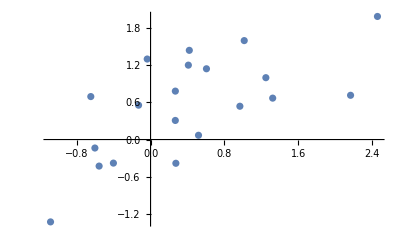

```mathematica
data=RandomVariate[
MultinormalDistribution[({{1, 0.7}, {0.7, 1}})],
20
];
ListPlot[data]
```

Fit the data with a 1^st order polynomial. The data can be specified in the matrix format of LinearModelFit or the Rule (→) based format used by Predict and NetTrain. The function returns an association that contains all relevant information about the model:

```mathematica
model = BayesianLinearRegression[data,{1,x},x];
Keys[model]
```

{LogEvidence,PriorParameters,PosteriorParameters,Posterior,Prior,Basis,IndependentVariables}

The logevidence is used for model selection and the prior and posterior parameters are the fundamental quantities from which all other relevant distributions are derived. Note the values used for the prior: if not prior is specified by the user, a weakly informative prior is automatically chosen so that all prior distributions are still normalised:

```mathematica
TableForm@Normal@N@model[[{"LogEvidence","PriorParameters","PosteriorParameters"}]]
```

LogEvidence→-31.229
PriorParameters→<|B→{0.,0.},Lambda→{{0.01,0.},{0.,0.01}},LambdaInverse→{{100.,0.},{0.,100.}},V→0.01,Nu→0.01|>
PosteriorParameters→<|B→{0.321205,0.574086},Lambda→{{20.01,8.48501},{8.48501,19.6675}},LambdaInverse→{{0.0611644,-0.0263878},{-0.0263878,0.0622297}},V→7.2244,Nu→20.01|>

The "Prior" and "Posterior" keys hold 4 distributions:

```mathematica
TableForm@Normal[Keys/@model[[{"Prior","Posterior"}]]]
```

Prior→{RegressionCoefficientDistribution,ErrorDistribution,PredictiveDistribution,UnderlyingValueDistribution}
Posterior→{RegressionCoefficientDistribution,ErrorDistribution,PredictiveDistribution,UnderlyingValueDistribution}

Visualise the prior predictive distribution to verify that the prior does not impose significant restrictions on the data:

```mathematica
Show[
Plot[Evaluate@InverseCDF[model["Prior","PredictiveDistribution"],{0.95,0.5,0.05}],
{x,-3,3},Filling->{1->{2},3-> {2}}, PlotLegends->Table[Quantity[i,"Percent"],{i,{95,50,5}}]
],
ListPlot[data],
PlotRange->All]
```

-Graphics-

Next, plot the posterior predictive distribution to inspect the regression. Note that the regression is specified in terms of a StudentTDistribution that depends on x. The function InverseCDF is convenient for extracting the prediction bands from the distribution:

StudentTDistribution[0.321205+0.574086 x,0.600865 √(1.06116-0.0527756 x+0.0622297 x^2),2001/100]

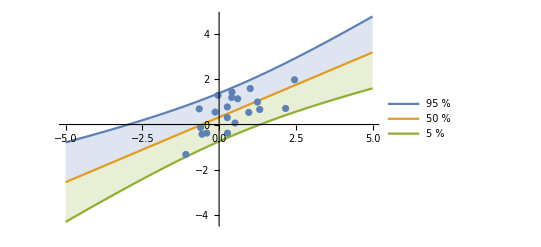

```mathematica
With[{
predictiveDist=model["Posterior","PredictiveDistribution"],
bands={95,50,5}
},
Print[predictiveDist];
Show[
Plot[
Evaluate@InverseCDF[predictiveDist,bands/100],
{x,-5,5},Filling->{1->{2},3-> {2}}, PlotLegends->Table[Quantity[i,"Percent"],{i,bands}]
],
ListPlot[data],
PlotRange->All
]
]
```

These bands can also be plotted with regressionPlot1D:

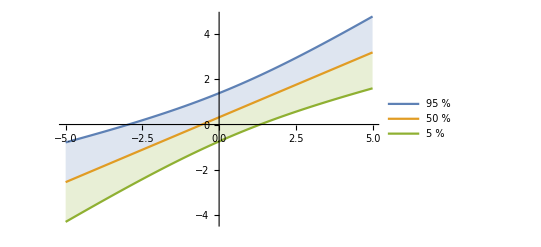

```mathematica
regressionPlot1D[model["Posterior","PredictiveDistribution"], {x,-5,5},{95, 50, 5}(* last argument can be omitted, in which case it defaults to {95, 50, 5}*)]
```

The fitted model is of the form y == a + b x + ϵ with ϵ\[Distributed]NormalDistribution[0, σ]. We can also show the fitted values of a + b x, taking into account the uncertainties in a and b, but without the error term ϵ:

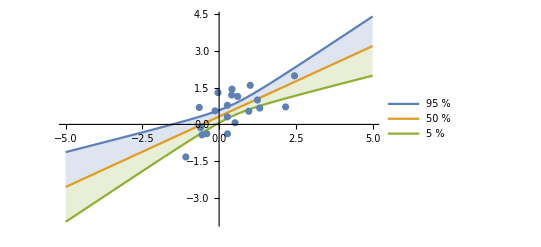

```mathematica
Show[regressionPlot1D[model["Posterior","UnderlyingValueDistribution"], {x,-5,5}],
ListPlot[data]
]
```

Visualise the joint distribution of the coefficients a and b:

MultivariateTDistribution[{0.321205,0.574086},{{0.0220828,-0.00952703},{-0.00952703,0.0224674}},2001/100]

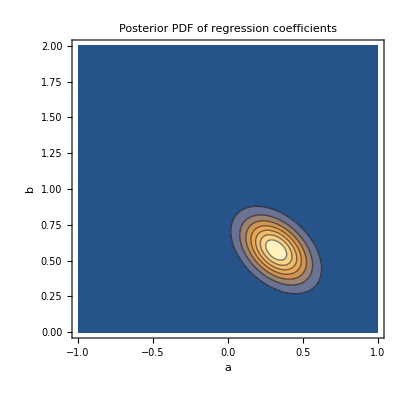

```mathematica
With[{
coefficientDist = model["Posterior","RegressionCoefficientDistribution"]
},
Print[coefficientDist];
ContourPlot[
Evaluate[PDF[coefficientDist,{a,b}]],
{a,-1,1},
{b,0,2},
PlotRange->{0,All},PlotPoints->20,FrameLabel->{"a","b"},ImageSize->400,
PlotLabel->"Posterior PDF of regression coefficients"
]
]
```

Plot the pdf of the posterior variance of the residuals:

InverseGammaDistribution[2001/200,3.6122]

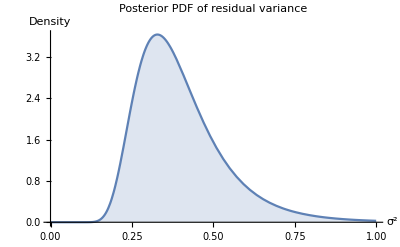

```mathematica
With[{
errDist = model["Posterior","ErrorDistribution"]
},
Print[errDist];
Quiet@Plot[
Evaluate[PDF[errDist,e]],
{e,0,1},
PlotRange->{0,All},AxesLabel->{"σ^2","Density"},ImageSize->400,
Filling->Axis,
PlotLabel->"Posterior PDF of residual variance"
]
]
```

Note that only the marginal distributions of the regression coefficients and variance are given since there is currently no convenient mechanism for providing the joint distribution.

#### Model comparison of polynomial fits

The next question is what polynomial order is appropriate for the data. Judging by eye, a 1^st order fit is enough, but let’s be certain.

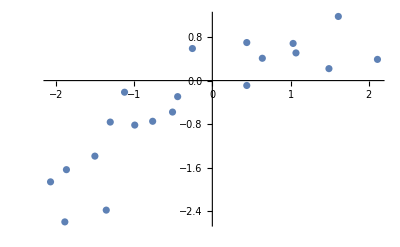

```mathematica
data=;
plot=ListPlot[data]
```

Fit the data with a polynomial of arbitrary degree and compare the prediction bands and log-evidence of fits up to degree 4:

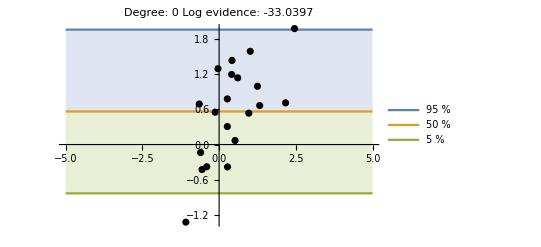
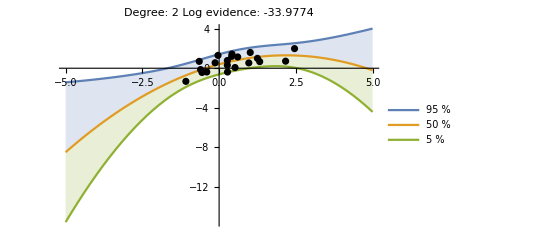
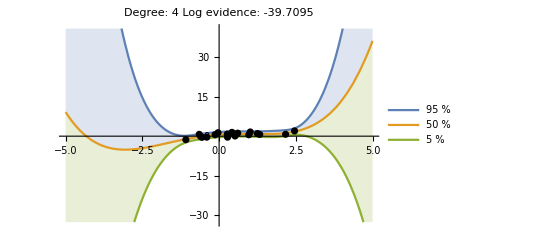
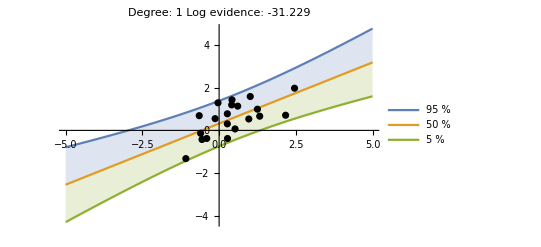
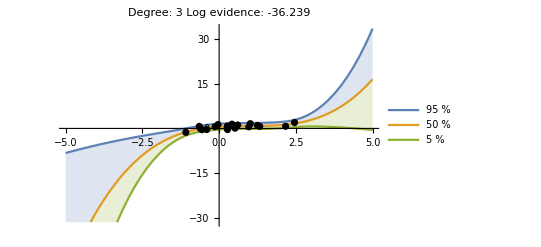
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- |

```mathematica
Multicolumn@Table[
Module[{
model=BayesianLinearRegression[Rule@@@data,x^Range[0,degree],x],
predictiveDist,
bands= {95,50,5}
},
predictiveDist=model["Posterior","PredictiveDistribution"];
Show[
regressionPlot1D[predictiveDist, {x,-5,5}],
ListPlot[data,PlotStyle->Black],
PlotRange->All,
PlotLabel-> StringForm["Degree: `1`\nLog evidence: `2`",degree,model["LogEvidence"] ]
]
],
{degree,0,4}
]
```

As can be seen, the logevidence supports the choice for a 1^st degree polynomial fit, though not always by much.

#### Mixture models

As the previous sections shows, it is not always clear which model is appropriate. Here is a deliberate example where it is unclear if the fit should be 1^st or 2^nd order:

```mathematica
data=;
plot=ListPlot[data]
```

-Graphics-

Fit the data with polynomials up to 4^th degree, rank the log-evidences and inspect them. The 1^st and 2^nd order fits are almost equally likely:

```mathematica
models=AssociationMap[
BayesianLinearRegression[Rule@@@data,x^Range[0,#],x]&,
Range[0,4]
];
ReverseSort@models[[All,"LogEvidence"]]
```

<|1→-29.8961,2→-29.9747,3→-34.2235,4→-38.4624,0→-38.8485|>

Instead of picking one of the models, we can define a mixture over all of them. First calculate the weights for each fit:

```mathematica
weights=Normalize[
(* subtract the max to reduce rounding error *)
Exp[models[[All,"LogEvidence"]]-Max[models[[All,"LogEvidence"]]]],
Total
];
ReverseSort[weights]
```

<|1→0.516002,2→0.47702,3→0.0068122,4→0.0000982526,0→0.0000667854|>

Define a mixture of posterior predictive distributions:

```mathematica
mixDist=MixtureDistribution[
Values[weights],
Values@models[[All,"Posterior","PredictiveDistribution"]]
];
Short/@mixDist
```

MixtureDistribution[{0.0000667854,0.516002,0.47702,0.0068122,0.0000982526},{«1»}]

Compare the mixture fit to the individual polynomial regressions. The mixture fit inherits features mainly from the two best models:

```mathematica
TabView[
KeyValueMap[
#1-> Show[
regressionPlot1D[#2,{x,-5,5},
PlotLabel->Replace[
Lookup[weights,#1,None],
n_?NumericQ:>StringForm["Weight: `1`", n]
]
],
plot
]&,
Prepend[
models[[All,"Posterior","PredictiveDistribution"]],
"Mixture"-> mixDist
]
]
]
```

123456

### Multivariate regression

BayesianLinearRegression can do multivariate regression. For example, generate some 3D data:

```mathematica
data = RandomVariate[
MultinormalDistribution[{0,0,2},RandomVariate[InverseWishartMatrixDistribution[5,IdentityMatrix[3]]]],
50
];
ListPointPlot3D[data]
```

-Graphics3D-

Instead of regression the z coordinate against x and y, it’s also possible to do a regression where the x coordinate is treated as the independent variable and y and z are both dependent on x:

```mathematica
multiModel=BayesianLinearRegression[data[[All,1]]-> data[[All,{2,3}]],{1,x},x];
multiModel["Posterior"]
```

<|RegressionCoefficientDistribution→MatrixTDistribution[{{0.0392016,2.25054},{-0.176528,-0.62506}},{{0.0202879,-0.00180316},{-0.00180316,0.0111389}},{{8.03963,4.40702},{4.40702,11.9327}},5001/100],ErrorDistribution→InverseWishartMatrixDistribution[5101/100,{{8.03963,4.40702},{4.40702,11.9327}}],PredictiveDistribution→MultivariateTDistribution[{0.0392016-0.176528 x,2.25054-0.62506 x},{{0.164022-0.000579754 x+0.0017907 x^2,0.0899107-0.000317799 x+0.000981593 x^2},{0.0899107-0.000317799 x+0.000981593 x^2,0.243448-0.000860493 x+0.00265782 x^2}},5001/100],UnderlyingValueDistribution→MultivariateTDistribution[{0.0392016-0.176528 x,2.25054-0.62506 x},{{0.00326149-0.000579754 x+0.0017907 x^2,0.00178783-0.000317799 x+0.000981593 x^2},{0.00178783-0.000317799 x+0.000981593 x^2,0.00484083-0.000860493 x+0.00265782 x^2}},5001/100]|>

The predictive joint distribution for y and z is a MultivariateTDistribution and the regression coefficients follow a MatrixTDistribution:

```mathematica
multiRegressionDist=multiModel["Posterior","PredictiveDistribution"]
multiModel["Posterior","RegressionCoefficientDistribution"]
```

MultivariateTDistribution[{0.0392016-0.176528 x,2.25054-0.62506 x},{{0.164022-0.000579754 x+0.0017907 x^2,0.0899107-0.000317799 x+0.000981593 x^2},{0.0899107-0.000317799 x+0.000981593 x^2,0.243448-0.000860493 x+0.00265782 x^2}},5001/100]

MatrixTDistribution[{{0.0392016,2.25054},{-0.176528,-0.62506}},{{0.0202879,-0.00180316},{-0.00180316,0.0111389}},{{8.03963,4.40702},{4.40702,11.9327}},5001/100]

Visualize the joint distribution as an animation:

```mathematica
ListAnimate[
Table[
ContourPlot[
Evaluate[PDF[multiRegressionDist,{y,z}]],
{y,-3,3},
{z,-3,3},
PlotRange->All,
FrameLabel->{"y","z"},
PlotLabel->StringForm["x = `1`",x],
PlotPoints->20
],
{x,-1.5,1.5,0.1}
],
AnimationRunning->False
]
```

### Options of BayesianLinearRegression

IncludeConstantBasis

Just like LinearModelFit, BayesianLinearRegression constructs a model with bias term by default:

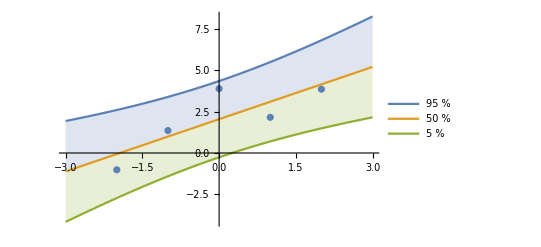

```mathematica
data=Range[-2,2]-> Range[-2,2]+1+RandomVariate[NormalDistribution[],5];
model=BayesianLinearRegression[data,x,x];
Show[
regressionPlot1D[model["Posterior","PredictiveDistribution"],{x,-3,3}],
ListPlot[Transpose[List@@data]]
]
```

Force the intercept to be zero:

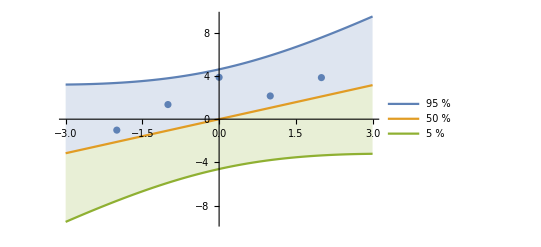

```mathematica
model2=BayesianLinearRegression[data,x,x,IncludeConstantBasis-> False];
Show[
regressionPlot1D[model2["Posterior","PredictiveDistribution"],{x,-3,3}],
ListPlot[Transpose[List@@data]]
]
```

“PriorParameters”

The prior can be specified in the same format as the parameter outputs of the BayesianLinearRegression. This can be used to update a model with new observations. To illustrate this, generate some test data and divide the dataset into 2 parts:

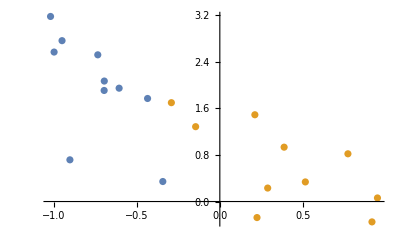

```mathematica
data =TakeDrop[ SortBy[First]@RandomVariate[MultinormalDistribution[{0,1},({{1, -1.3}, {-1.3, 2}})],20],10];
plot=ListPlot[data]
```

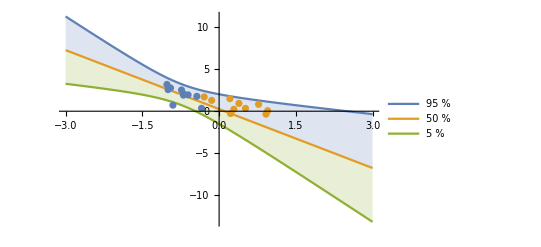

```mathematica
model1=BayesianLinearRegression[data[[1]],x,x];
Show[
regressionPlot1D[model1["Posterior","PredictiveDistribution"],{x,-3,3}],
plot
]
```

Use the posterior parameters of model1 as the prior to update the model with the 2^nd half of the dataset:

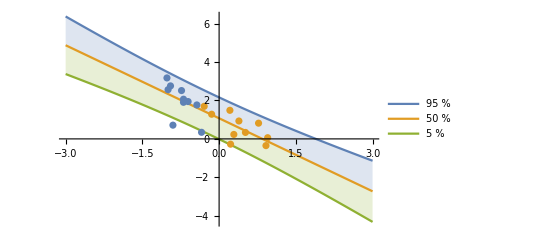

```mathematica
model2=BayesianLinearRegression[data[[2]],x,x,"PriorParameters"-> model1["PosteriorParameters"]];
Show[
regressionPlot1D[model2["Posterior","PredictiveDistribution"],{x,-3,3}],
plot
]
```

The result is exactly the same as when you would fit all of the data in a single step:

```mathematica
model3=BayesianLinearRegression[Join@@data,x,x];
Column[{
model3["PosteriorParameters"],
model2["PosteriorParameters"]
}]
```

<|B→{1.07289,-1.26736},Lambda→{{20.01,-3.5575},{-3.5575,8.98088}},LambdaInverse→{{0.0537611,0.0212958},{0.0212958,0.119783}},V→7.54387,Nu→2001/100|>
<|B→{1.07289,-1.26736},Lambda→{{20.01,-3.5575},{-3.5575,8.98088}},LambdaInverse→{{0.0537611,0.0212958},{0.0212958,0.119783}},V→7.54387,Nu→2001/100|>

“IncludeFunctions”

When "IncludeFunctions"→True, the returned association contains the key "Functions". This key holds the functions that can be used to generate distributions from arbitrary values of hyperparameters:

```mathematica
data=Range[-2,2]-> Range[-2,2]+RandomVariate[NormalDistribution[],5];
model=BayesianLinearRegression[data,x,x,"IncludeFunctions"->True];
Keys@model["Functions"]
```

{RegressionCoefficientDistribution,ErrorDistribution,PredictiveDistribution,UnderlyingValueDistribution}

```mathematica
model["Functions","PredictiveDistribution"]
```

Simplify[StudentTDistribution[{1,x}.#B,√((#V ({1,x}.#LambdaInverse.{1,x}+1))/(#Nu)),#Nu]]&

The posterior distribution was obtained by applying predictive distribution function to the posterior parameters:

```mathematica
model["Functions","PredictiveDistribution"]@model["PosteriorParameters"]===model["Posterior","PredictiveDistribution"]
```

True

### Fully symbolic results

BayesianLinearRegression can generate symbolic results for univariate regression problems. For example, calculate the predictive posterior after a single observation for any prior (this can take a few minutes):

```mathematica
model=BayesianLinearRegression[{xobs->yobs},x,x,"PriorParameters"-><|"B"->{b1,b2},"Lambda"->{{l11^2,r l11 l22},{r l11 l22,l22}},"V"->v,"Nu"->nu|>];
dist[{xobs_,yobs_},{b1_,b2_},{l11_,l22_,r_},v_,nu_] = Assuming[
v>0&&nu>0&&{xobs,yobs,x,b1,b2,l11,l22}∈Reals&&-1<r<1,
FullSimplify[model["Posterior","PredictiveDistribution"]]
]
```

StudentTDistribution[(b1 l11 (l11 l22 (-1+l22 r^2)+l22 r xobs-l11 xobs^2)+x (b2 l22 (-1+l11 (-l11+l11 l22 r^2+r xobs))+l11 (-l22 r+l11 xobs) (b1-yobs))-l22 (-1+l11 r xobs) (b2 xobs-yobs))/(l22 (-1+l11^2 (-1+l22 r^2))+2 l11 l22 r xobs-l11^2 xobs^2),√(-(((x^2 (1+l11^2)+2 l22-2 l11 l22 r xobs+xobs^2-2 x (l11 l22 r+xobs)+l11^2 (l22-l22^2 r^2+xobs^2)) (b1^2 l11^2 l22 (-1+l22 r^2)-l11^2 v xobs^2+2 b1 l11^2 l22 (-1+l22 r^2) (b2 xobs-yobs)+l11^2 l22^2 r^2 (v+(-b2 xobs+yobs)^2)-l22 (v (1+l11^2-2 l11 r xobs)+l11^2 (-b2 xobs+yobs)^2)))/((1+nu) (-l11^2 l22^2 r^2+l11^2 xobs^2+l22 (1+l11^2-2 l11 r xobs))^2))),1+nu]

Visualize the prediction bands:

```mathematica
Manipulate[
regressionPlot1D[
dist[pt,b,{√l11,√l22,r},v,nu],
{x,-10,10},
PlotRange->{-20,20},
ImageSize->Large
],
{{pt,{0,0}},{-10,-10},{10,10},ControlType-> Locator},
{{b,{0,0}},{-10,-10},{10,10}},
{{l11,0.01},0.0001,0.1},
{{l22,0.01},0.0001,0.1},
{{r,0},-1,1},
{{v,0.1},0.0001,1},
{{nu,0.1},0.0001,1},
SaveDefinitions->True
]
```

## Bayesian neural networks

This section implements ideas discussed in the following blog post: 
["https://blog.wolfram.com/2018/05/31/how-optimistic-do-you-want-to-be-bayesian-neural-network-regression-with-prediction-errors/"](https://blog.wolfram.com/2018/05/31/how-optimistic-do-you-want-to-be-bayesian-neural-network-regression-with-prediction-errors/)

See also:
["http://mlg.eng.cam.ac.uk/yarin/blog_3d801aa532c1ce.html"](http://mlg.eng.cam.ac.uk/yarin/blog_3d801aa532c1ce.html)
["http://www.cs.ox.ac.uk/people/yarin.gal/website/thesis/thesis.pdf"](http://www.cs.ox.ac.uk/people/yarin.gal/website/thesis/thesis.pdf)
["https://arxiv.org/pdf/1703.02914.pdf"](https://arxiv.org/pdf/1703.02914.pdf)

### Examples

First make some test data:

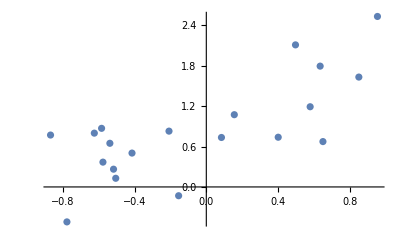

{0.634779→1.79573,-0.777161→-0.519519,0.579052→1.19191,-0.624394→0.79963,-0.517278→0.263886,-0.868522→0.771412,0.0844932→0.735196,-0.537691→0.648829,-0.207988→0.82956,0.400948→0.738974,-0.576348→0.368782,0.497314→2.11164,-0.154299→-0.130628,-0.50501→0.128742,0.954344→2.53395,0.650326→0.674282,0.85055→1.6331,0.156112→1.07392,-0.414261→0.503429,-0.583898→0.871136}

```mathematica
BlockRandom[
SeedRandom[1];
testdata=(#-> (#+2 RandomReal[]))&/@RandomReal[{-1,1},20];
ListPlot[List@@@testdata]
]
testdata
```

The main function used for constructing Bayesian-style regression neural networks is regressionLossNet.

The first argument can take one of two values: "HeteroScedastic" (default value if omitted) or "HomoScedastic". A heteroscedastic will allow the predicted variance of the network to be dependent on the network inputs whereas a homoscedastic network will predict a constant variance.

There are several options for specifying the network architecture:

```mathematica
Options[regressionLossNet]
```

{NetworkDepth→4,LayerSize→100,ActivationFunction→SELU,DropoutProbability→0.25,BatchNormalization→False,Input→Automatic,LossModel→Automatic}

"NetworkDepth" and "LayerSize" specify the complexity of the network.

"ActivationFunction" specifies the nonlinearity used in the ElementWiseLayers in the network. The default is the "ScaledExponentialLinearUnit" activation.

"DropoutProbability" specifies the dropout probability in the DropoutLayers. Default value is 0.25. Setting "DropoutProbability"→ None leaves them out completely.

"BatchNormalization" takes the values True or False (default). If True, BatchNormalizationLayers will be used in the network.

"Input" specifies the dimensions of the input data.

"LossModel" is used to specify the network loss. There are 2 possible values:

Automatic (default). This value uses the Gaussian negative loglikelihood as the loss function

{"AlphaDivergence","Alpha"→ α,"SampleNumber"→n} uses the alpha-divergence loss developed by Li and Gal (["https://arxiv.org/abs/1703.02914"](https://arxiv.org/abs/1703.02914)). The default values are α=0.5 and n=10. The larger the value of α, the less the network will be penalized for occasionally producing wrong predictions when sampled with dropout layers active. Thus, a network trained at a higher value of α will produce predictions with greater variance and is therefore more conservative/pessimistic in its estimates. Special values for α are -∞, 0 and ∞. The function alphaDivergenceLoss is used to produce the loss layer for the alpha-divergence:

```mathematica
alphaDivergenceLoss[0.5(*Alpha*)] (* Infer dimension of input vector automatically *)
alphaDivergenceLoss[0.5(*Alpha*), "Input" -> {20} (* 20 samples.*)]
alphaDivergenceLoss[-Infinity]
alphaDivergenceLoss[0]
alphaDivergenceLoss[Infinity]
```

Examples of networks:

```mathematica
regressionLossNet[]
regressionLossNet["HomoScedastic"]
regressionLossNet["LossModel"-> {"AlphaDivergence","Alpha"->0.5,"SampleNumber"->20}]
```

Train a network (note the necessity of specifying LossFunction→"Loss")

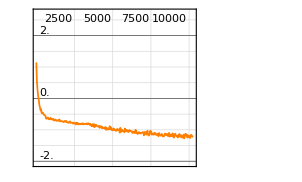
NetTrain Results
summary | ,,  batches:10266  rounds:10266  time:1.0min  examples/s:3422
data | ,,  training examples:20  processed examples:205320  skipped examples:0
method | ,,  ADAMoptimizer  batch size20GPU
round | ,,  loss:-1.05
 | rounds
loss | -Graphics- | 
 |

```mathematica
lambda2=0.01;
trainedNet=NetTrain[
regressionLossNet["HeteroScedastic",
"NetworkDepth"->4,"LayerSize"->100,
"ActivationFunction"->"SELU","DropoutProbability"->0.25,"BatchNormalization"->True,
"LossModel"-> {"AlphaDivergence","Alpha"-> 0.5,"SampleNumber"->20}],
testdata,
All,
LossFunction->"Loss",
Method->{"ADAM","L2Regularization"-> lambda2},
TimeGoal->60,
TargetDevice->"GPU"
]
```

Use the function extractRegressionNet to get the regression net back out of the trained net. Note that the BatchNormalizationLayers will be replaced by constant layers that perform the same operation (the function batchnormToChain does this) because BatchNormalizationLayer doesn’t work correctly when making predictions with NetEvaluationMode→ "Train".

```mathematica
?batchnormToChain
extractRegressionNet[trainedNet]
```

Generate predictions from the network in the range x∈Interval[{-1,1}] by sampling each input 500 times with the DropoutLayers active to account for the uncertainty in the network weights. In other words, the generated distributions account for both model variance and uncertainty in the network weights.

```mathematica
sampleTrainedNet[trainedNet,Range[-1,1,0.1],500,TargetDevice-> "GPU"]
```

<|-1.→NormalDistribution[0.469493,0.910846],-0.9→NormalDistribution[0.470954,0.694819],-0.8→NormalDistribution[0.467173,0.56388],-0.7→NormalDistribution[0.467608,0.407553],-0.6→NormalDistribution[0.473636,0.322741],-0.5→NormalDistribution[0.45112,0.321078],-0.4→NormalDistribution[0.443898,0.361925],-0.3→NormalDistribution[0.42535,0.387403],-0.2→NormalDistribution[0.416261,0.447045],-0.1→NormalDistribution[0.431088,0.388968],0.→NormalDistribution[0.491948,0.231797],0.1→NormalDistribution[0.797632,0.0379798],0.2→NormalDistribution[1.06942,0.231235],0.3→NormalDistribution[1.26314,0.385074],0.4→NormalDistribution[1.34776,0.48676],0.5→NormalDistribution[1.48028,0.564627],0.6→NormalDistribution[1.5663,0.645388],0.7→NormalDistribution[1.6622,0.723416],0.8→NormalDistribution[1.68152,0.810263],0.9→NormalDistribution[1.72945,0.807173],1.→NormalDistribution[1.79283,0.844182]|>

Plot the predictions:

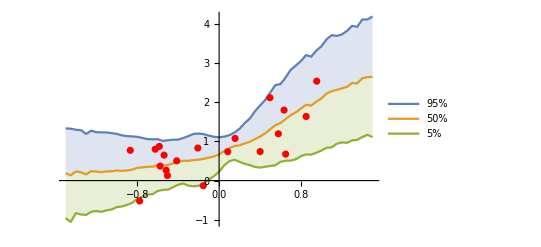

```mathematica
With[{xValues=Range[-1.5,1.5,0.05],quantiles={0.95,0.5,0.05}},
Show[
ListPlot[
Transpose[
Values[InverseCDF[#,quantiles]&/@sampleTrainedNet[trainedNet,xValues,500,TargetDevice-> "GPU"]]
],
Joined->True,
DataRange->MinMax[xValues],
Filling->{1->{2},3->{2}},
PlotLegends->Map[StringForm["`1`%",#]&,Round[100 * quantiles]]
],
ListPlot[List@@@testdata,PlotStyle->Red],
PlotRange-> All
]
]
```

Compute the approximate Bayesian logevidence (also known as “marginal likelihood”) of the network model. It is given by marginal LogLikelihood[data] - L2RegularizationLoss[net]. The higher the log evidence, the better the model represents the data.

```mathematica
networkLogEvidence[trainedNet,testdata,lambda2,TargetDevice-> "GPU"]
```

0.773003

If you want to see how the logevidence depends on the regularisation coefficient, simply pass it as a symbol:

```mathematica
networkLogEvidence[trainedNet,testdata,λ,TargetDevice-> "GPU"]
```

1.11002-25.0995 λ

Perform a comparative analysis of several networks. You can run the cell below several times to aggregate the results. Note that the L2Regularization can be interpreted as a prior on the length scale of the variations in the data, so we consider it as a parameter that either has to be fixed a-priori or determined by cross-validation.

```mathematica
If[!ListQ[result],result={}];
result=Flatten@{
TakeLargestBy[result,#LogEvidence&,UpTo[5]], (*retain up to 5 best networks from previous runs*)
ParallelTable[
With[{
config=<|
"ErrorModel"-> RandomChoice[{"HomoScedastic","HeteroScedastic"}],
"L2Regularization"-> 0.01,
"DropoutProbability"-> 0.25,
"LayerSize"->RandomInteger[{10,200}],
"NetworkDepth"-> RandomInteger[{1,5}],
"ActivationFunction"-> RandomChoice[{Ramp,"SELU",Tanh}]
|>
},
With[{
net=NetTrain[
regressionLossNet[
config["ErrorModel"],##,
"LossModel"-> {"AlphaDivergence","Alpha"-> 0.5,"SampleNumber"->20}
]&@@FilterRules[Normal[config],Options[regressionLossNet]],
testdata,All,
LossFunction->"Loss",
Method->{"ADAM","L2Regularization"-> config["L2Regularization"]},
TimeGoal->60,TargetDevice->"GPU",
TrainingProgressReporting->None
]
},
Join[config,
<|
"Network"-> net,
"LogEvidence"-> networkLogEvidence[net,testdata,{λ,config["L2Regularization"]},TargetDevice-> "GPU"]
|>
]
]
],
{12},
Method->"CoarsestGrained",
DistributedContexts->All
]
};
```

View the hyperparameters corresponding to the highest logevidence:

```mathematica
TableForm@With[{assocs=TakeLargestBy[KeyDrop[result,"Network"],#LogEvidence[[2]]&,UpTo[10]]},
Prepend[Values[assocs],Keys[First[assocs]]]
]
```

ErrorModel | L2Regularization | DropoutProbability | LayerSize | NetworkDepth | ActivationFunction | LogEvidence
HeteroScedastic | 0.01 | 0.25 | 47 | 2 | Ramp | 1.73056-45.3654 λ
1.27691
HeteroScedastic | 0.01 | 0.25 | 196 | 1 | Ramp | 1.37819-34.5553 λ
1.03263
HeteroScedastic | 0.01 | 0.25 | 136 | 3 | SELU | 1.38328-43.248 λ
0.950804
HeteroScedastic | 0.01 | 0.25 | 108 | 5 | SELU | 1.50456-58.1659 λ
0.9229
HomoScedastic | 0.01 | 0.25 | 111 | 5 | Ramp | 1.31521-42.4791 λ
0.890417
HeteroScedastic | 0.01 | 0.25 | 88 | 5 | Tanh | 1.24254-39.593 λ
0.846606
HeteroScedastic | 0.01 | 0.25 | 90 | 2 | Tanh | 0.885213-29.5956 λ
0.589256
HomoScedastic | 0.01 | 0.25 | 17 | 2 | SELU | 0.705763-11.8689 λ
0.587074
HeteroScedastic | 0.01 | 0.25 | 123 | 5 | Tanh | 0.846027-27.7367 λ
0.56866
HeteroScedastic | 0.01 | 0.25 | 121 | 1 | Tanh | 0.807089-29.7886 λ
0.509203

Show the predictions of the top 5 networks together.

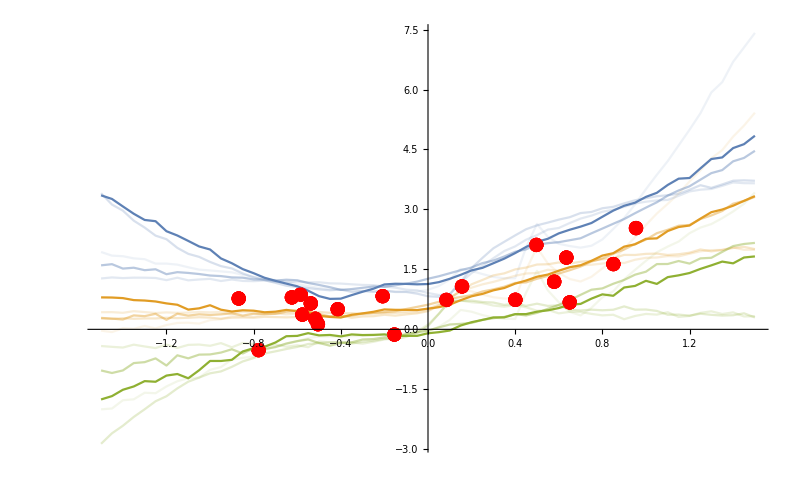

```mathematica
Show@Module[{
xValues=Range[-1.5,1.5,0.05],
quantiles={0.95,0.5,0.05},
 results = TakeLargestBy[result,#LogEvidence[[2]]&,UpTo[5]],
minMaxEvidence 
},
minMaxEvidence = MinMax[results[[All,"LogEvidence",2]]];
Show[
ListPlot[
Thread@Tooltip[
Transpose[
Values[InverseCDF[#,quantiles]&/@sampleTrainedNet[#Network,xValues,500,TargetDevice-> "GPU"]]
],
#LogEvidence[[2]]
],
Joined->True,
DataRange->MinMax[xValues],
PlotStyle->Opacity[Rescale[#["LogEvidence"][[2]],minMaxEvidence,{0.1,1}]]
],
ListPlot[List@@@testdata,PlotStyle->Red],
PlotRange-> All,
ImageSize->800
]&/@Reverse[results]
]
```